## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/mercury/MoM-plots/";  
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/mercury/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.146314 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.0.0 for Mac OS X x86

date: Apr 19, 2020, time: 21:20:44

nb: /Users/dantopa/Mathematica_files/nb/ert/mercury/MoM-plots/meanRCS-plots-01.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.146314 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
ipad=ImagePadding->{{Automatic,3},{Automatic,Automatic}};
```

```mathematica
isize=ImageSize->5 72;
```

#### functions

#### substitutions

#### modules

## master color scheme

### import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
σ=RotateLeft[meanRCS,180];
{m,n}=Dimensions[σ]
```

{28,361}

```mathematica
mx=Max[meanRCS]
mn=Min[meanRCS]
```

59.2522

0.798997

## 1

### setup

```mathematica
θticks={{1,"-180°"},{91,"-90°"},{181,"0°"},{271,"90°"},{361,"180°"}};
```

```mathematica
Clear[fticks];
fticks:={{Automatic,Automatic},{θticks,Automatic}};
```

### plot utility

```mathematica
Clear[myPlotter];
myPlotter[ψ_,str_String,options___]:=Module[{g},
g=ArrayPlot[Reverse[ψ],
options,
ColorFunction->(Hue[(1-Rescale[#,{mn,mx}])magicnumber]&),
ColorFunctionScaling->False,
FrameTicks->{{{1,3},{8,10},{18,20},{28,30}},θticks,{{1,100},{4,50},{8,30},{13,20},{18,15},{28,10}},None},
FrameLabel->{"Frequency ν, MHZ","Yaw α","Wavelength λ, m",None},
PlotLabel->str,
AspectRatio->1/GoldenRatio
]]
```

```mathematica
(* PlotLegends->Placed[Automatic,After]] *)
```

## 2

```mathematica
meanRCS=Import[dirData<>"mean-total-rcs-02.dat"];
σ=RotateLeft[meanRCS,180];
{m,n}=Dimensions[σ]
```

{28,180}

```mathematica
θticks={{1,"-180°"},{n/4,"-90°"},{n/2,"0°"},{(3n)/4,"90°"},{n,"180°"}};
```

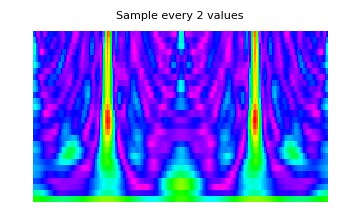

```mathematica
g002=myPlotter[meanRCS,"Sample every 2 values",isize]
```

```mathematica
Export[dirGraph<>"sampling-02.png",g002]
```

## 4

```mathematica
meanRCS=Import[dirData<>"mean-total-rcs-04.dat"];
σ=RotateLeft[meanRCS,180];
{m,n}=Dimensions[σ]
```

{28,90}

```mathematica
θticks={{1,"-180°"},{n/4,"-90°"},{n/2,"0°"},{(3n)/4,"90°"},{n,"180°"}};
```

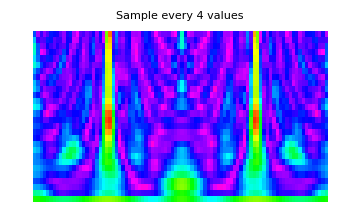

```mathematica
g020=myPlotter[meanRCS,"Sample every 4 values",isize]
```

## 12

```mathematica
meanRCS=Import[dirData<>"mean-total-rcs-12.dat"];
σ=RotateLeft[meanRCS,180];
{m,n}=Dimensions[σ]
```

{28,30}

```mathematica
θticks={{1,"-180°"},{n/4,"-90°"},{n/2,"0°"},{(3n)/4,"90°"},{n,"180°"}};
```

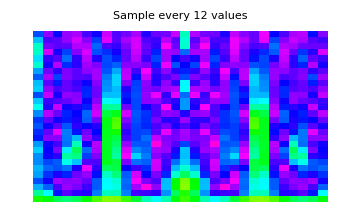

```mathematica
g020=myPlotter[meanRCS,"Sample every 12 values",isize]
```

## 20

```mathematica
meanRCS=Import[dirData<>"mean-total-rcs-20.dat"];
σ=RotateLeft[meanRCS,180];
{m,n}=Dimensions[σ]
```

{28,18}

```mathematica
θticks={{1,"-180°"},{n/4,"-90°"},{n/2,"0°"},{(3n)/4,"90°"},{n,"180°"}};
```

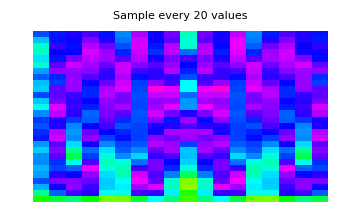

```mathematica
g020=myPlotter[meanRCS,"Sample every 20 values",isize]
```

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```